# BH to WH Transition

## Regular black hole : 0<a<r_H=1

```mathematica
Quit[];
```

```mathematica
Clear["Global`*"];
```

## Definitions

## Metric & V_eff definitions

```mathematica
(* mass fixed such r_horizon = 1 *)
m=(√(1+a^2) (1+a^2+9 leta^2))/(24 leta^2)+1/8 leta ArcTan[(√(1+a^2))/leta];
```

```mathematica
(*metric*) 
F[x_]:=SetPrecision[(3 -(8 m)/x+x^2/(3 leta^2)+leta/x ArcTan[x/leta]),20];
(*I dont include the minus sign on the gtt definition *)
gtt[x_]:=SetPrecision[ 1/4 F[√(x^2+a^2)],20];
grr[x_]:= SetPrecision[((x^2+a^2+2 leta^2)^2)/((x^2+a^2+leta^2)^2 F[√(x^2+a^2)]),20];
(**)
gθθ[x_]:=SetPrecision[x^2+a^2,20];
p[x_]:=SetPrecision[ √gθθ[x],20];
PsiSquare[x_]:=SetPrecision[-ε/(8 π leta^2)*(x^2 grr[x])/(x^2+leta^2),20];
(*useful definitions (for "easier" calculations) *)
(*h[x_]:=SetPrecision[√(gtt[x]/grr[x]),20];*)
(* η=-leta^2/ε;*)

(*potential*)
Veff[x_,lam_]:= Evaluate[SetPrecision[gtt[x]/p[x]^2 lam(lam+1)+1/(2 grr[x]^2 p[x])( 2 gtt[x] grr [x] D[p[x],{x,2}]+grr[x]  D[gtt[x],x]  D[p[x],x] -gtt[x] D[grr[x],x]   D[p[x],x] )  ,100]] ;
```

## Mass s.t. r_H=1

```mathematica
m=Solve[3 -(8 m)/(√(a^2+r^2))+(a^2+r^2)/(3 leta^2)+leta/(√(a^2+r^2))ArcTan[(√(a^2+r^2))/leta]==0/.r-> 1,m,Reals][[1,1,2]]//Simplify
```

(√(1+a^2) (1+a^2+9 leta^2))/(24 leta^2)+1/8 leta ArcTan[(√(1+a^2))/leta]

```mathematica
m/.a->0//Simplify
```

1/24 (9+1/leta^2+3 leta ArcTan[1/leta])

```mathematica
horSol[#,0]&/@{1,2,483}
```

{{{r→-1.},{r→1.}},{{r→-1.},{r→1.}},{{r→-1.},{r→1.}}}

Tortoise Not working properly when using the below definitions(??!!!??)

```mathematica
mass[leta_,a_]:=mass[leta,a]=(√(1+a^2) (1+a^2+9 leta^2))/(24 leta^2)+1/8 leta ArcTan[(√(1+a^2))/leta];
```

```mathematica
Clear[m]
```

```mathematica
Print[gtt[r]]
```

0.25 (3.-(8. m)/(√(a^2+r^2))+(0.33333333333333333333 (a^2+r^2))/leta^2+(leta ArcTan[(√(a^2+r^2))/leta])/(√(a^2+r^2)))

```mathematica
horizonsol[letain_,ain_]:=
NumberForm[NSolve[3 -(8 m)/(√(r^2+a^2))+(r^2+a^2)/(3 leta^2)+leta/(√(r^2+a^2))ArcTan[(√(r^2+a^2))/leta]==0/.leta->letain/.a->ain,r,Reals],200][[1,2,1,2]]
```

```mathematica
horizonsol[1,#]&/@{0.1,0.2,0.5,0.9}
```

{1.,1.,1.,1.}

## Plot Functions

## plotfunc functions (for a & leta) + ploshowfunc definitions

----------  DOCUMENTATION  -----------

plotalphafunc : Takes 3 arguments ( value, List[3elements], value ). Provide leta value,  a List with 3 values 				for alpha , & a value for lambda.  The function will define 3 plots (with fixed legend 					positions) named V1,V2,V3 for the 3  different  values of alpha. The legend display values are 				automatically updated

                     ------------------------------------------------------------------------------------------
                     
 plotshowfunc :Takes 2 (list) arguments ( { horiz_range }, { vertical_range }) .Provide the 								range({horizontal},{vertical} ) takes automatically the 3 plots defined by the  							“plotalphafunc” function and shows them together in a single image. 
           
                      ------------------------------------------------------------------------------------------
                      
 plotletafunc : (almost identical with plotalphafunc) Takes 3 arguments ( value, List[3elements], value ). 				Provide alpha value,  a List with 3 values for leta , & a value for lambda.  The function will 				define 3 plots (with fixed legend positions) named V1,V2,V3 for the 3  different  values of 					alpha. The legend display values are automatically updated
 
 --------------------------------------------

```mathematica
(*  
StringTemplate["α = ``"][alist3values[[1]]]  *)
```

```mathematica
plotalphafunc[letain_,alist3values_,lambdain_]:=Block[{ε=1,leta=letain},
times=50;
(**)
Block[{a=alist3values[[1]]},
 V1=Plot[{Veff[r,lambdain]},{r,horizonsol[leta,a],times*horizonsol[leta,a]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["α = ``"][alist3values[[1]]],15]},{0.71,0.8}]},PlotStyle->colorlist[[1]],Frame->True];
];
(**)
Block[{a=alist3values[[2]]},
 V2=Plot[{Veff[r,lambdain]},{r,horizonsol[leta,a],times*horizonsol[leta,a]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["α = ``"][alist3values[[2]]],15]},{0.71,0.7}]},PlotStyle->colorlist[[2]],Frame->True];
];
(**)
Block[{a=alist3values[[3]]},
 V3=Plot[{Veff[r,lambdain]},{r,horizonsol[leta,a],times*horizonsol[leta,a]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["α = ``"][alist3values[[3]]],15]},{0.71,0.6}]},PlotStyle->colorlist[[3]],Frame->True];
];
];
```

Example

```mathematica
plotalphafunc[5,List[0.2,0.4,0.9],0]
```

```mathematica
plotshowfunc[horizontalrange_,verticalrange_]:=Show[{V1,V2,V3},PlotRange->{horizontalrange,verticalrange}(*{{1,10},{0,0.12}}*),ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

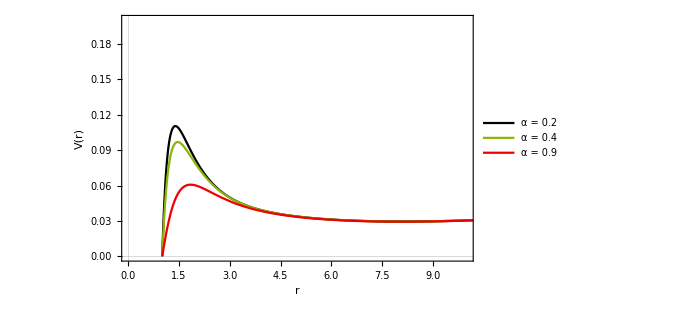

```mathematica
plotshowfunc[{0,10},{0,0.2}]
```

```mathematica
plotletafunc[ain_,letalist3values_,lambdain_]:=Block[{ε=1,a=ain},
times=50;
(**)
Block[{leta=letalist3values[[1]]},
 V1=Plot[{Veff[r,lambdain]},{r,horizonsol[leta,a],times*horizonsol[leta,a]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["ℓ_η = ``"][letalist3values[[1]]],15]},{0.71,0.8}]},PlotStyle->colorlist[[1]],Frame->True];
];
(**)
Block[{leta=letalist3values[[2]]},
 V2=Plot[{Veff[r,lambdain]},{r,horizonsol[leta,a],times*horizonsol[leta,a]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["ℓ_η = ``"][letalist3values[[2]]],15]},{0.71,0.7}]},PlotStyle->colorlist[[2]],Frame->True];
];
(**)
Block[{leta=letalist3values[[3]]},
 V3=Plot[{Veff[r,lambdain]},{r,horizonsol[leta,a],times*horizonsol[leta,a]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["ℓ_η = ``"][letalist3values[[3]]],15]},{0.71,0.6}]},PlotStyle->colorlist[[3]],Frame->True];
];
];
```

Example

```mathematica
plotletafunc[0.5,{3,5,10},0]
```

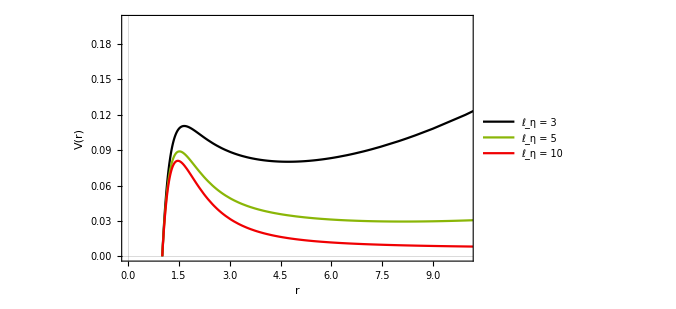

```mathematica
plotshowfunc[{0,10},{0,0.2}]
```

## Colors for plots

```mathematica
CD3 = ColorData[3,"ColorList"];
colorlist= CD3[[#]]& /@{1,4,6,3};
newred=ColorData[16,"ColorList"][[9]];
colorlist =  Insert[colorlist,newred,3]//Append[ColorData[14,"ColorList"][[2]]]
```

{RGBColor[0., 0., 0.],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.9411764705882353, 0., 0.00784313725490196],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744]}

```mathematica
{RGBColor[0., 0., 0.],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.9411764705882353, 0., 0.00784313725490196],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882]}
```

```mathematica
ColorData[#,"ColorList"]& /@ Range[13,20]
```

{{RGBColor[0.6588235294117647, 0.4980392156862745, 0.49019607843137253],RGBColor[0.7215686274509804, 0.1843137254901961, 0.050980392156862744],RGBColor[0.803921568627451, 0.5450980392156862, 0.4588235294117647],RGBColor[0.8156862745098039, 0.6901960784313725, 0.6313725490196078],RGBColor[0.9490196078431372, 0.8745098039215686, 0.7176470588235294],RGBColor[0.3803921568627451, 0.3843137254901961, 0.6352941176470588],RGBColor[0.23137254901960785, 0.20784313725490197, 0.5529411764705883],RGBColor[0.5843137254901961, 0.5607843137254902, 0.6627450980392157],RGBColor[0.4666666666666667, 0.27450980392156865, 0.34901960784313724],RGBColor[0.596078431372549, 0.27450980392156865, 0.36470588235294116]},{RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744],RGBColor[1., 0.7333333333333333, 0.2],RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076],RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547],RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039],RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157],RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529],RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392],RGBColor[0.8549019607843137, 0.19607843137254902, 0.27450980392156865]},{RGBColor[0.40784313725490196, 0.15294117647058825, 0.13725490196078433],RGBColor[0.6588235294117647, 0.5607843137254902, 0.5333333333333333],RGBColor[0.8313725490196079, 0.43529411764705883, 0.12941176470588237],RGBColor[0.8941176470588236, 0.8274509803921568, 0.7647058823529411],RGBColor[0.9372549019607843, 0.7764705882352941, 0.3137254901960784],RGBColor[0.23921568627450981, 0.27058823529411763, 0.4627450980392157],RGBColor[0.23529411764705882, 0.1450980392156863, 0.4588235294117647],RGBColor[0.36470588235294116, 0.23921568627450981, 0.43137254901960786],RGBColor[0.2196078431372549, 0.12549019607843137, 0.18823529411764706],RGBColor[0.5529411764705883, 0.12941176470588237, 0.2235294117647059],RGBColor[0.7058823529411765, 0.2627450980392157, 0.27058823529411763]},{RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882],RGBColor[0.6784313725490196, 0.3137254901960784, 0.],RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765],RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941],RGBColor[0.8549019607843137, 0.9607843137254902, 1.],RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333],RGBColor[0.6392156862745098, 0.5607843137254902, 0.7529411764705882],RGBColor[0.1450980392156863, 0.11372549019607843, 0.16470588235294117],RGBColor[0.9411764705882353, 0., 0.00784313725490196]},{RGBColor[0.2823529411764706, 0.22745098039215686, 0.2235294117647059],RGBColor[0.5647058823529412, 0.23137254901960785, 0.15294117647058825],RGBColor[0.6392156862745098, 0.39215686274509803, 0.3333333333333333],RGBColor[0.8627450980392157, 0.6196078431372549, 0.2627450980392157],RGBColor[0.9647058823529412, 0.788235294117647, 0.5254901960784314],RGBColor[0.4588235294117647, 0.592156862745098, 0.4627450980392157],RGBColor[0.23921568627450981, 0.45098039215686275, 0.24705882352941178],RGBColor[0.34509803921568627, 0.5803921568627451, 0.6901960784313725],RGBColor[0.1843137254901961, 0.39215686274509803, 0.49019607843137253],RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608]},{RGBColor[0.7647058823529411, 0.5568627450980392, 0.5411764705882353],RGBColor[0.9921568627450981, 0.788235294117647, 0.7568627450980392],RGBColor[0.29411764705882354, 0.19215686274509805, 0.10588235294117647],RGBColor[0.37254901960784315, 0.2784313725490196, 0.19215686274509805],RGBColor[0.29411764705882354, 0.27058823529411763, 0.18823529411764706],RGBColor[0.7098039215686275, 0.6980392156862745, 0.5058823529411764],RGBColor[0.8705882352941177, 0.8784313725490196, 0.6901960784313725],RGBColor[0.27058823529411763, 0.33725490196078434, 0.28627450980392155],RGBColor[0.6980392156862745, 0.43529411764705883, 0.4470588235294118]},{RGBColor[0.5686274509803921, 0.043137254901960784, 0.],RGBColor[0.5607843137254902, 0.22745098039215686, 0.2],RGBColor[0.6627450980392157, 0.3333333333333333, 0.],RGBColor[0.8470588235294118, 0.6392156862745098, 0.42745098039215684],RGBColor[0.7686274509803922, 0.4627450980392157, 0.14901960784313725],RGBColor[0.01568627450980392, 0.19215686274509805, 0.09803921568627451],RGBColor[0.19215686274509805, 0.3686274509803922, 0.27450980392156865],RGBColor[0.4, 0.5254901960784314, 0.4588235294117647],RGBColor[0.06666666666666667, 0.15294117647058825, 0.20784313725490197]},{RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],RGBColor[0.9019607843137255, 0.19607843137254902, 0.12941176470588237],RGBColor[0.3568627450980392, 0.054901960784313725, 0.01568627450980392],RGBColor[0.6823529411764706, 0.41568627450980394, 0.],RGBColor[0.8352941176470589, 0.6274509803921569, 0.08627450980392157],RGBColor[0.9803921568627451, 0.7803921568627451, 0.25882352941176473],RGBColor[1., 0.9058823529411765, 0.6549019607843137],RGBColor[0.3843137254901961, 0.6, 0.8784313725490196],RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],RGBColor[0.12549019607843137, 0.36470588235294116, 0.6784313725490196]}}

## Analysis & FD Code Setup

## tortoise

### Regular black hole : 0<a<r_H=1

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
leta=1;a=0.7;ε=1;(*η=-leta^2/ε;*) 
(**)
x= First[x1/. NDSolve[{x1'[xstar]==((1/4(3 -(8 m)/(√(x1[xstar]^2+a^2))+(x1[xstar]^2+a^2)/(3 leta^2)+leta/(√(x1[xstar]^2+a^2))ArcTan[(√(x1[xstar]^2+a^2))/leta]))/(((x1[xstar]^2+a^2+2 leta^2)^2)/((x1[xstar]^2+a^2+leta^2)^2)(1/(3 -(8 m)/(√(x1[xstar]^2+a^2))+(x1[xstar]^2+a^2)/(3 leta^2)+leta/(√(x1[xstar]^2+a^2))ArcTan[(√(x1[xstar]^2+a^2))/leta]))) )^(1/2),x1[0]==(*throat @ x=0*)SetPrecision[1.1*horizonsol[leta,a],200]},
x1,{xstar,-1000,500},Method->Automatic,
InterpolationOrder->All]]
{xstarmin,xstarmax}=InterpolatingFunctionDomain[x][[1]]
x[#]& /@{xstarmin,xstarmax}
```

NDSolve::ndsz: At xstar == 4.35348, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

{-1000.,4.35348}

{1.,3.80559×10^12}

## Further checking r_*vs V_eff

### General

Now we just check the general behavior of the r(r_*) function and how it may affect the V_eff

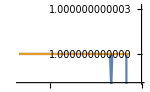
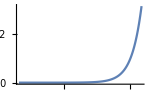

```mathematica
(*r[rstar_]=r[rstar]/.First[Out[12]];*)
Row[{Plot[{x[xstar],horizonsol[leta,a]},{xstar,-200,-20},PlotRange->Automatic,ImageSize->150],
Plot[{x[xstar]},{xstar,-10,1},PlotRange->All,ImageSize->150]}]
```

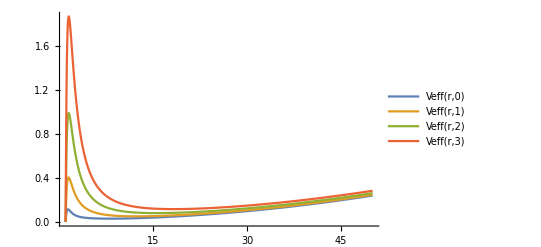

```mathematica
Block[{leta=5,a=0.1,ε=1 },
(*Clear[η];
η=-leta^2/ε;
horSol=NumberForm[NSolve[3 -(8 m)/(√(r^2))+r^2/(3 leta^2)+leta/(√(r^2))ArcTan[(√(r^2))/leta]==0,r,Reals],20];
 horizon=SetPrecision[r/.horSol[[1,2,1]],20];*)
VrPlot=Plot[{Veff[r,0],Veff[r,1],Veff[r,2],Veff[r,3]},{r,horizonsol[leta,a],50},PlotRange->All(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"]]
```

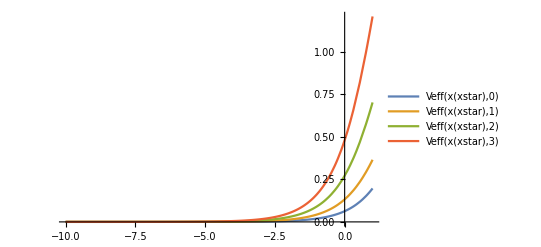

```mathematica
Block[{leta=1,a=0.9,ε=1 },
(*Clear[η];
η=-leta^2/ε;
horSol=NumberForm[NSolve[3 -(8 m)/(√(r^2))+r^2/(3 leta^2)+leta/(√(r^2))ArcTan[(√(r^2))/leta]==0,r,Reals],20];
 horizon=SetPrecision[r/.horSol[[1,2,1]],20];*)
VrPlot=Plot[{Veff[x[xstar],0],Veff[x[xstar],1],Veff[x[xstar],2],Veff[x[xstar],3]},{xstar,-10,1},PlotRange->All(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"]]
```

So...The effective potential develops discontinuities for at the negative range of xstar... the x[xstar] does not , it is well behaved.

### leta/alpha plots + plotfunc definition

Plot  wrt alpha

```mathematica
horizonsol[#,1]&/@{0.1,1,2,5}
```

{1.,1.,1.,1.}

```mathematica
(*  
StringTemplate["α = ``"][alist3values[[1]]]  *)
```

```mathematica
plotfunc[letain_,alist3values_,lambdain_]:=Block[{ε=1,leta=letain},
times=50;
(**)
Block[{a=alist3values[[1]]},
 V1=Plot[{Veff[r,lambdain]},{r,horizonsol[leta,a],times*horizonsol[leta,a]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["α = ``"][alist3values[[1]]],15]},{0.71,0.8}]},PlotStyle->colorlist[[1]],Frame->True];
];
(**)
Block[{a=alist3values[[2]]},
 V2=Plot[{Veff[r,lambdain]},{r,horizonsol[leta,a],times*horizonsol[leta,a]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["α = ``"][alist3values[[2]]],15]},{0.71,0.7}]},PlotStyle->colorlist[[2]],Frame->True];
];
(**)
Block[{a=alist3values[[3]]},
 V3=Plot[{Veff[r,lambdain]},{r,horizonsol[leta,a],times*horizonsol[leta,a]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["α = ``"][alist3values[[3]]],15]},{0.71,0.6}]},PlotStyle->colorlist[[3]],Frame->True];
];
];
```

plots for leta=5 a=0.1, 0.5 , 0.7

```mathematica
plotfunc[5,List[0.2,0.4,0.9],0]
```

```mathematica
plotshowfunc[horizontalrange_,verticalrange_]:=Show[{V1,V2,V3},PlotRange->{horizontalrange,verticalrange}(*{{1,10},{0,0.12}}*),ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
plotshowfunc[{0,10},{0,0.2}]
```

-Graphics-

Small mass/ bigger leta ---> positive barrier

### Mass Plots ( + responses )

Plots wrt to mass

#### Leta = 0.1 , m = 0.005, 0.01 ,0.025 - echoes - , 0.03, 0.04, 0.07, 0.1- QNringdown , 0.5 , 0.7 - exponential falloff

```mathematica
Clear[leta,m]
horSol=NumberForm[NSolve[3 -(8 m)/(√(r^2))+r^2/(3 leta^2)+leta/(√(r^2))ArcTan[(√(r^2))/leta]==0/.leta->0.1/.m->0.005,r,Reals],20];
 horizon=SetPrecision[r/.horSol[[1,2,1]],20]
```

0.0099999503556164257012

```mathematica
Block[{ε=1,leta=0.1},
times=10;
V1=Plot[{Veff[r,2]/. m->0.005 },{r,0.0099999503,(times+40)*0.0099999503},PlotRange->All,PlotLegends->{Placed[{Style["m=0.005",15,FontFamily->"Times New Roman"]},{0.8,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
 V2=Plot[{Veff[r,2]/. m->0.01 },{r,0.019998445,(times+15)*0.019998445},PlotRange->All,PlotLegends->{Placed[{Style["m=0.01",15,FontFamily->"Times New Roman"]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];V3=Plot[{Veff[r,2]/. m->0.025 },{r,0.04986878,times*0.04986878},PlotRange->All,PlotLegends->{Placed[{Style["m=0.025",15,FontFamily->"Times New Roman"]},{0.8,0.54}]},PlotStyle->colorlist[[3]],Frame->True];]
```

```mathematica
Show[{V1,V2,V3},PlotRange->{{0.001,0.48},{100,6000}},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

copy paste the corresponding time evolution just to have the whole picture .

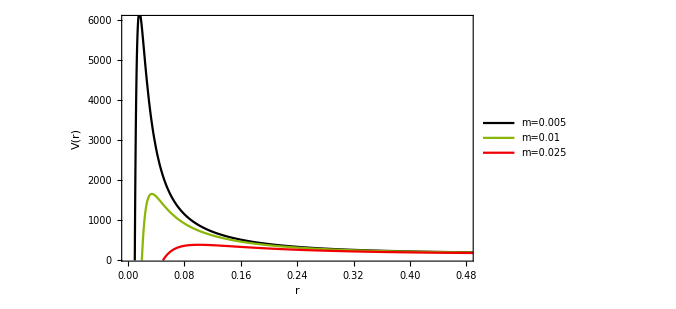
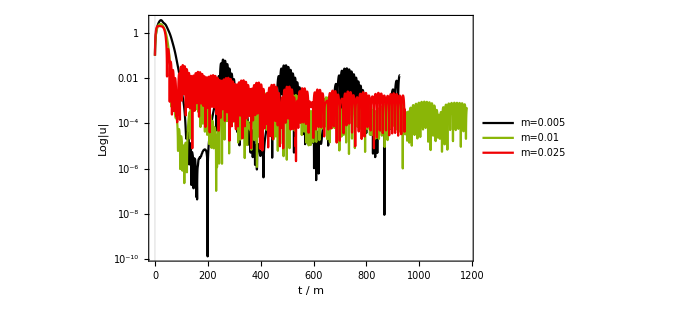

```mathematica
Block[{ε=1,leta=0.1},
times=20;
V1=Plot[{Veff[r,2]/. m->0.005 },{r,0.0099999503,(times+300)*0.0099999503},PlotRange->All,PlotLegends->{Placed[{Style["m=0.005",15,FontFamily->"Times New Roman"]},{0.81,0.86}]},PlotStyle->colorlist[[1]],Frame->True];
V4=Plot[{Veff[r,2]/. m->0.03 },{r,0.05969668,100*0.05969668},PlotTheme->"Scientific",PlotRange->All,PlotLegends->{Placed[{Style["m=0.03",15,FontFamily->"Times New Roman"]},{0.8,0.78}]},PlotStyle->colorlist[[2]],Frame->True];
V5=Plot[{Veff[r,2]/. m->0.04 },{r,0.07893018,100 *0.07893018},PlotTheme->"Scientific",PlotRange->All,PlotLegends->{Placed[{Style["m=0.04",15,FontFamily->"Times New Roman"]},{0.6,0.78}]},PlotStyle->colorlist[[2]],Frame->True];
V6=Plot[{Veff[r,2]/. m->0.05},{r,0.09734999,200 *0.09734999},PlotTheme->"Scientific",PlotRange->All,PlotLegends->{Placed[{Style["m=0.05",15,FontFamily->"Times New Roman"]},{0.8,0.70}]},PlotStyle->colorlist[[3]],Frame->True];

V7=Plot[{Veff[r,2]/. m->0.07 },{r,0.1310361,40 *0.1310361},PlotTheme->"Scientific",PlotRange->All,PlotLegends->{Placed[{Style["m=0.07",15,FontFamily->"Times New Roman"]},{0.8,0.62}]},PlotStyle->colorlist[[4]],Frame->True];
V8=Plot[{Veff[r,2]/. m->0.1 },{r,0.17359827,50 * 0.17359826},PlotTheme->"Scientific",PlotRange->All,PlotLegends->{Placed[{Style["m=0.1",15,FontFamily->"Times New Roman"]},{0.78,0.86}]},PlotStyle->colorlist[[4]],Frame->True];
V9=Plot[{Veff[r,2]/. m->0.5 },{r,0.42651917,times * 0.42651917},PlotTheme->"Scientific",PlotRange->All,PlotLegends->{Placed[{Style["m=0.5",15,FontFamily->"Times New Roman"]},{0.78,0.78}]},PlotStyle->colorlist[[5]],Frame->True];
]
```

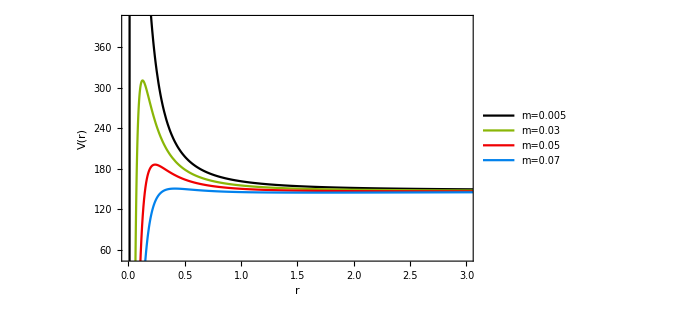
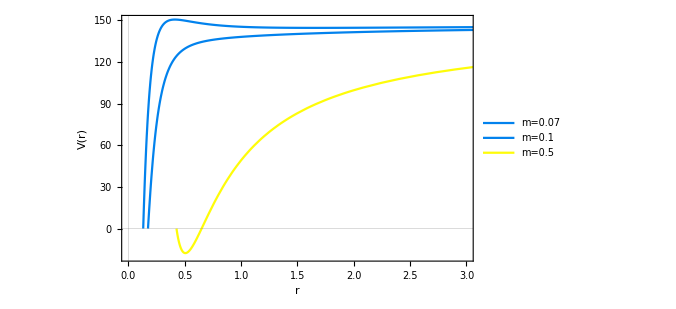

```mathematica
Row[{Show[{V1,V4,V6,V7},PlotRange->{{0,3},{50,400}},ImageSize->500,FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White],
Show[{V7,V8,V9},PlotRange->{{0,3},{-20,150}},ImageSize->500,FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]}]
```

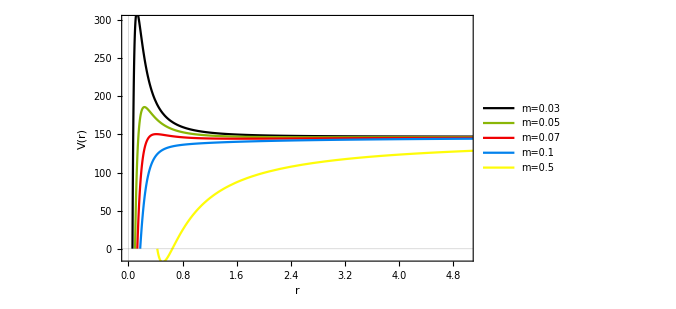

copy paste the corresponding time evolution just to have the whole picture .

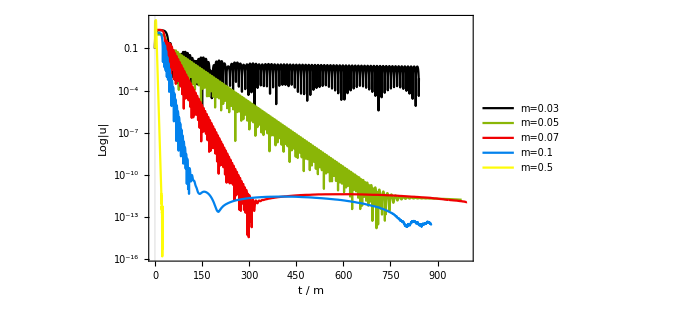

#### Leta = 1 , m = 2,2.5,2.75,3 qnm transition to exp.falloff + 100, 200, 500 - exponential falloff

```mathematica
Clear[leta,m]
horSol=NumberForm[NSolve[3 -(8 m)/(√(r^2))+r^2/(3 leta^2)+leta/(√(r^2))ArcTan[(√(r^2))/leta]==0/.leta->1/.m->2,r,Reals],20];
 horizon=SetPrecision[r/.horSol[[1,2,1]],20]
```

{{InterpolatingFunction[{{-10000.000000000000000, 1.0230242295509136225}}, <>]→-2.711770676263161},{InterpolatingFunction[{{-10000.000000000000000, 1.0230242295509136225}}, <>]→2.711770676263161}}

2.7117706762631614836

```mathematica
horizonsol[m_,leta_]:=horizonsol[m,leta]=SetPrecision[r/.NSolve[3 -(8 m)/(√(r^2))+r^2/(3 leta^2)+leta/(√(r^2))ArcTan[(√(r^2))/leta]==0,r,Reals][[2,1]],10];(* event horizon radius *)
```

```mathematica
Block[{ε=1,leta=1},
times=20;
V1=Plot[{Veff[r,2]/. m->100 },{r,13.156,(times+50)*13.156},PlotRange->All,PlotLegends->{Placed[{Style["m=100",15,FontFamily->"Times New Roman"]},{0.8,0.40}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/. m->200 },{r,16.685,(times+20) *16.685},PlotRange->All,PlotLegends->{Placed[{Style["m=200",15,FontFamily->"Times New Roman"]},{0.8,0.30}]},PlotStyle->colorlist[[2]],Frame->True];
V3=Plot[{Veff[r,2]/. m->500},{r,22.7603,times *22.7603},PlotRange->All,PlotLegends->{Placed[{Style["m=500",15,FontFamily->"Times New Roman"]},{0.8,0.20}]},PlotStyle->colorlist[[3]],Frame->True];
]
```

```mathematica
Show[{V1,V2,V3},PlotRange->{{0,400},{-20,2}},ImageSize->500,FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

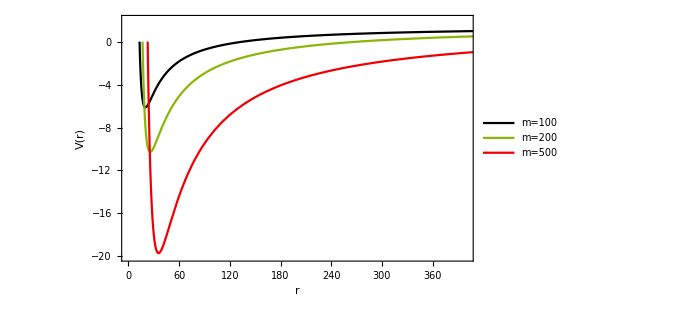
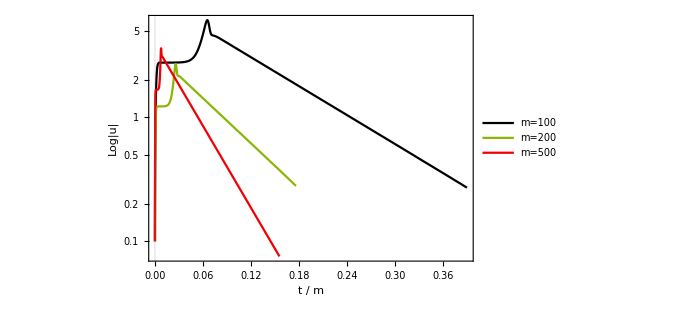

```mathematica
Block[{ε=1,leta=1},
times=50;
V1=Plot[{Veff[r,2]/. m->2 },{r,horizonsol[2,leta],(times+100)*horizonsol[2,leta]},PlotRange->All,PlotLegends->{Placed[{Style["m=2",15,FontFamily->"Times New Roman"]},{0.85,0.60}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/. m->2.5 },{r,horizonsol[2.5,leta],(times+30) *horizonsol[2.5,leta]},PlotRange->All,PlotLegends->{Placed[{Style["m=2.5",15,FontFamily->"Times New Roman"]},{0.86,0.52}]},PlotStyle->colorlist[[2]],Frame->True];
V3=Plot[{Veff[r,2]/. m->2.75},{r,horizonsol[2.75,leta],times *horizonsol[2.75,leta]},PlotRange->All,PlotLegends->{Placed[{Style["m=2.75",15,FontFamily->"Times New Roman"]},{0.87,0.44}]},PlotStyle->colorlist[[3]],Frame->True];
V4=Plot[{Veff[r,2]/. m->3},{r,horizonsol[3,leta],times *horizonsol[3,leta]},PlotRange->All,PlotLegends->{Placed[{Style["m=3",15,FontFamily->"Times New Roman"]},{0.85,0.36}]},PlotStyle->colorlist[[4]],Frame->True];
]
```

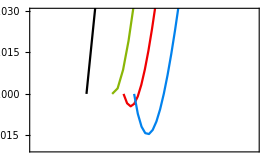

```mathematica
plotinset=Show[{V1,V2,V3,V4},PlotRange->{{2,5},{-0.02,0.03}},ImageSize->270,Frame->True,
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White,FrameStyle->Black,FrameTicks->{{True,False},{False,All}}]
```

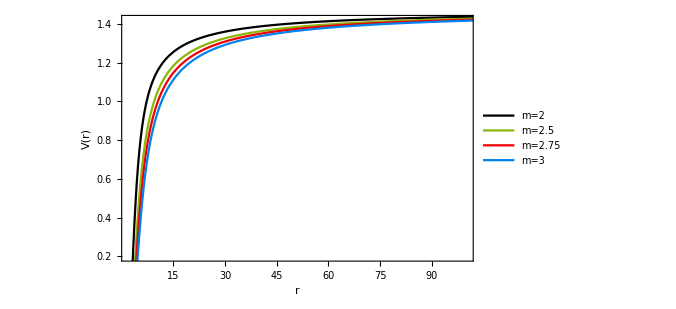

```mathematica
Show[{V1,V2,V3,V4},PlotRange->{{2,100},{0.2,1.42}},ImageSize->500,FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White,Epilog-> {Inset[plotinset,{75,0.95},Scaled[{1,1}]]}]
```

#### Leta = 5 , m = 0.1, 0.2, 0.5, 1- echoes -, 2, 5- QNringdown

```mathematica
Clear[leta,m]
horSol=NumberForm[NSolve[3 -(8 m)/(√(r^2))+r^2/(3 leta^2)+leta/(√(r^2))ArcTan[(√(r^2))/leta]==0/.leta->5/.m->0.2,r,Reals],20]
 horizon=SetPrecision[r/.horSol[[1,2,1]],20];
```

{{r→-0.3999991845346673},{r→0.3999991845346673}}

```mathematica
Block[{ε=1,leta=5},
times=20;
V1=Plot[{Veff[r,2]/. m->0.1 },{r,0.1999999,(times+50)*0.1999999},PlotRange->All,PlotLegends->{Placed[{Style["m=0.1",15,FontFamily->"Times New Roman"]},{0.8,0.40}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/. m->0.2 },{r,0.3999991,(times+20) *0.3999991},PlotRange->All,PlotLegends->{Placed[{Style["m=0.2",15,FontFamily->"Times New Roman"]},{0.8,0.30}]},PlotStyle->colorlist[[2]],Frame->True];
V3=Plot[{Veff[r,2]/. m->0.5},{r,0.9999222,times *0.9999222},PlotRange->All,PlotLegends->{Placed[{Style["m=0.5",15,FontFamily->"Times New Roman"]},{0.8,0.20}]},PlotStyle->colorlist[[3]],Frame->True];
]
```

```mathematica
Show[{V1,V2,V3},PlotRange->{{0,10},{0.7,15}},ImageSize->500,FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

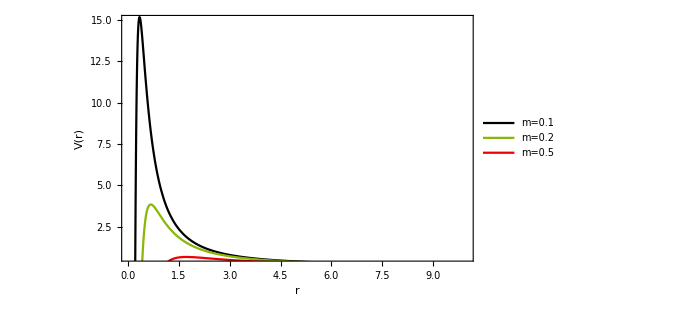
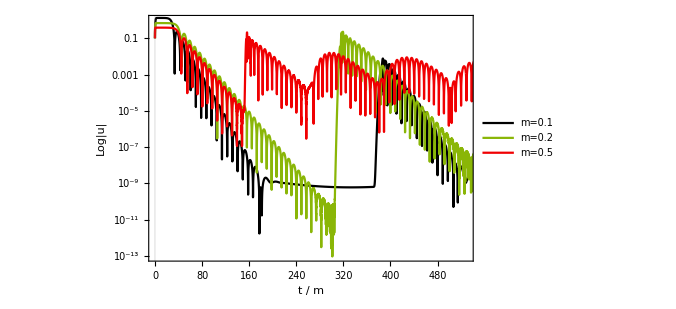

```mathematica
Block[{ε=1,leta=5},
times=20;
V4=Plot[{Veff[r,2]/. m->1 },{r,1.9977129,(times+66)*1.9977129},PlotRange->All,PlotLegends->{Placed[{Style["m=1",15,FontFamily->"Times New Roman"]},{0.8,0.60}]},PlotStyle->colorlist[[1]],Frame->True];
V5=Plot[{Veff[r,2]/. m->2 },{r,3.9465091,(times+24) *3.9465091},PlotRange->All,PlotLegends->{Placed[{Style["m=2",15,FontFamily->"Times New Roman"]},{0.8,0.50}]},PlotStyle->colorlist[[2]],Frame->True];
V6=Plot[{Veff[r,2]/. m->5},{r,8.6799133,times *8.6799133},PlotRange->All,PlotLegends->{Placed[{Style["m=5",15,FontFamily->"Times New Roman"]},{0.8,0.40}]},PlotStyle->colorlist[[3]],Frame->True];
]
```

```mathematica
Show[{V4,V5,V6},PlotRange->{{0,150},{0.01,0.21}},ImageSize->500,FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

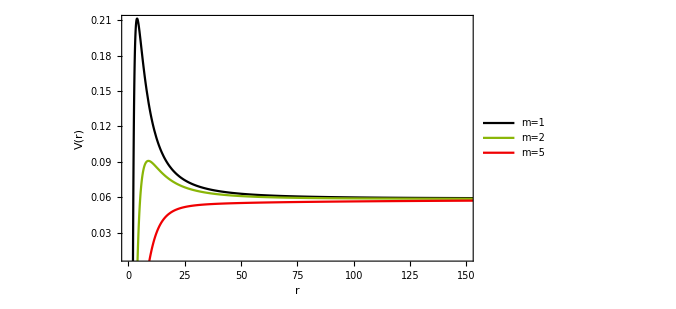
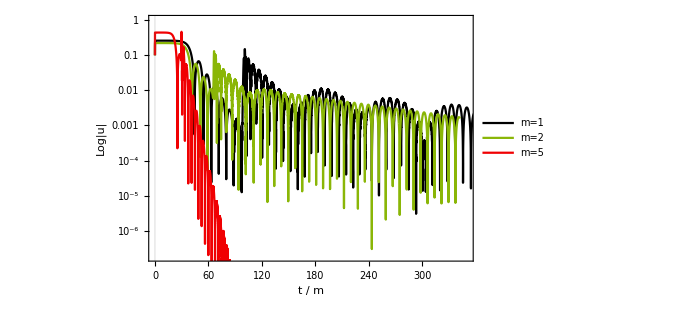

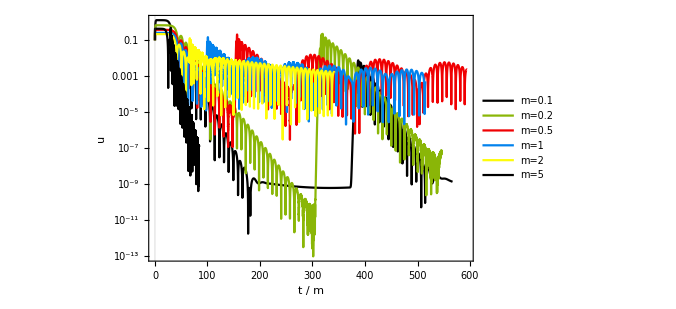

#### Leta = 100 , m = 0.1, 1 QNringdown

```mathematica
Clear[leta,m]
horSol=NumberForm[NSolve[3 -(8 m)/(√(r^2))+r^2/(3 leta^2)+leta/(√(r^2))ArcTan[(√(r^2))/leta]==0/.leta->100/.m->0.1,r,Reals],20]
 horizon=SetPrecision[r/.horSol[[1,2,1]],20];
```

{{r→-0.19999999999984},{r→0.19999999999984}}

```mathematica
Block[{ε=1,leta=100},
times=20;
V1=Plot[{Veff[r,2]/. m->0.1 },{r,0.1999999,(times+10)*0.1999999},PlotRange->All,PlotLegends->{Placed[{Style["m=0.1",15,FontFamily->"Times New Roman"]},{Scaled[{0.7,0.6}], {0,0}}]},PlotStyle->colorlist[[1]],Frame->True];
]
```

```mathematica
Show[{V1},PlotRange->{{0,5},{0.7,15}},ImageSize->500,FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

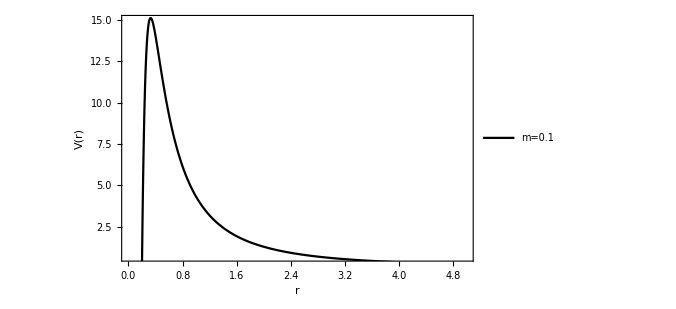
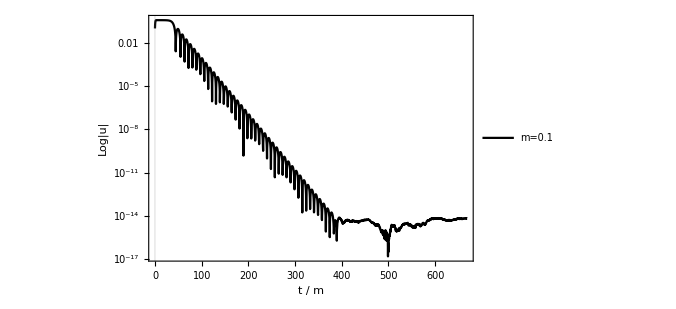

### lambda Plots

```mathematica
legendstyle={Style["ℓ=2",15],Style["ℓ=3",15],Style["ℓ=4",15],Style["ℓ=5",15]};
VstarPlot=Plot[{Veff[r[rstar],2],Veff[r[rstar],3],Veff[r[rstar],4],Veff[r[rstar],5]},{rstar,-54.7,54.7},PlotRange->All,PlotTheme->"Scientific" ,PlotStyle->colorlist ,PlotLegends->{ Placed[legendstyle,{0.15,0.5}]},
ImageSize->500];
```

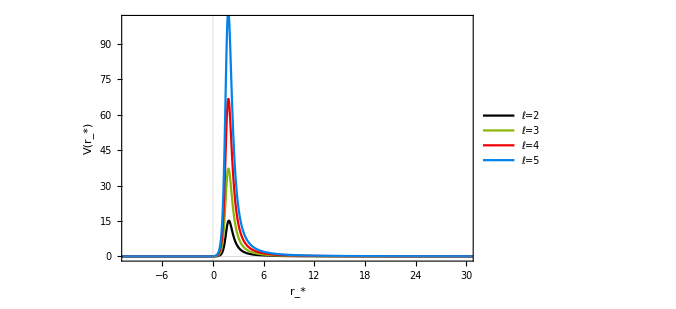

```mathematica
Show[VstarPlot, PlotRange->{{-10,30},{0,100}},
FrameLabel->{{HoldForm["V(r_*)" ],None},{HoldForm["r_*"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

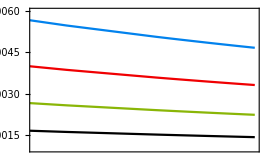

```mathematica
plotinset=Plot[{{Veff[r[rstar],2],Veff[r[rstar],3],Veff[r[rstar],4],Veff[r[rstar],5]}},{rstar,-54.7,150},
PlotRange->{{140,150},{0.0001,0.0006}},
PlotTheme->"Scientific",(*GridLines->{{etd,2 etd},None} ,GridLinesStyle->Directive[Black, Dashed,Thick],*)
PlotStyle->colorlist,Background->White,FrameStyle->Black,FrameTicks->{{True,False},{False,All}},
(*PlotLegends->{ Placed[LineLegend[{Style["l_η=0.8",15]}],{0.8,0.8}]},*)
ImageSize->270]
```

```mathematica
legendstyle={Style["ℓ=2",15],Style["ℓ=3",15],Style["ℓ=4",15],Style["ℓ=5",15]};
NewVstarPlot=Plot[{Veff[r[rstar],2],Veff[r[rstar],3],Veff[r[rstar],4],Veff[r[rstar],5]},{rstar,-54.7,54.7},PlotRange->All,PlotTheme->"Scientific",PlotStyle->colorlist ,PlotLegends->{ Placed[legendstyle,{0.15,0.5}]},
ImageSize->500,
Epilog-> {Inset[plotinset,{29,40},{150,0.0001},{65,60}]}];

Show[NewVstarPlot, PlotRange->{{-10,30},{0,100}},
FrameLabel->{{HoldForm["V(r_*)" ],None},{HoldForm["r_*"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

-Graphics-

Now wrt to r coordinate

```mathematica
horizonsol[m_,leta_]:=horizonsol[m,leta]=SetPrecision[r/.NSolve[3 -(8 m)/(√(r^2))+r^2/(3 leta^2)+leta/(√(r^2))ArcTan[(√(r^2))/leta]==0,r,Reals][[2,1]],20]
```

```mathematica
Block[{m=0.1,leta=100},
legendstyle={Style["ℓ=2",15],Style["ℓ=3",15],(*Style["ℓ=4",15],*)Style["ℓ=5",15]};
VstarPlot=Plot[{Veff[r,2],Veff[r,3],(*Veff[r,4],*)Veff[r,5]},{r,horizonsol[0.1,100],20*horizonsol[0.1,100]},PlotRange->All,PlotTheme->"Scientific" ,PlotStyle->colorlist ,PlotLegends->{ Placed[legendstyle,{0.3,0.75}]},
ImageSize->500];
]
```

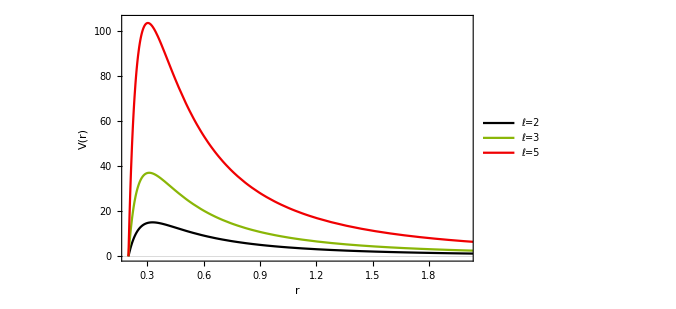

```mathematica
Show[VstarPlot, PlotRange->{{0.2,2},{0,105}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

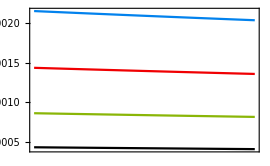

```mathematica
Block[{m=0.1,leta=100},plotinset=Plot[{{Veff[r,2],Veff[r,3],Veff[r,4],Veff[r,5]}},{r,1000*horizonsol[0.1,100],1050*horizonsol[0.1,100]},
PlotRange->Automatic,
PlotTheme->"Scientific",(*GridLines->{{etd,2 etd},None} ,GridLinesStyle->Directive[Black, Dashed,Thick],*)
PlotStyle->colorlist,Background->White,FrameStyle->Black,FrameTicks->{{True,False},{False,All}},
(*PlotLegends->{ Placed[LineLegend[{Style["l_η=0.8",15]}],{0.8,0.8}]},*)
ImageSize->270]
]
```

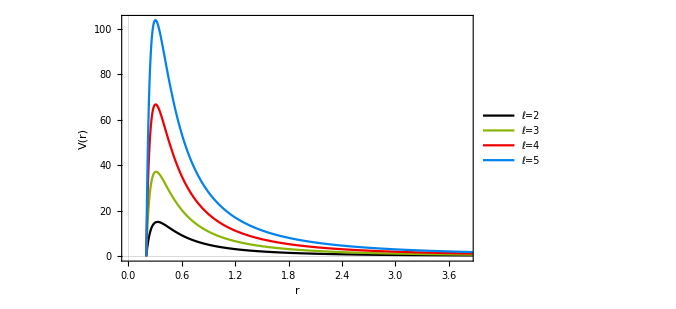

```mathematica
Block[{m=0.1,leta=100},
legendstyle={Style["ℓ=2",15],Style["ℓ=3",15],Style["ℓ=4",15],Style["ℓ=5",15]};
NewVstarPlot=Plot[{Veff[r,2],Veff[r,3],Veff[r,4],Veff[r,5]},{r,horizonsol[0.1,100],20*horizonsol[0.1,100]},PlotRange->All,PlotTheme->"Scientific" ,PlotStyle->colorlist ,PlotLegends->{ Placed[legendstyle,{0.3,0.66}]},
ImageSize->500,
Epilog-> {Inset[plotinset,{3.7,50},{210,0.0005},{65,60}]}];
]

Show[NewVstarPlot, PlotRange->{{0,3.8},Automatic},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

## horizon vs AdS radius (not modified)

Can observe a relation between the “percentage”= (AdSradius - rhorizon)/rhorizon== "free available space” and the occurence of the echoes ?

```mathematica
horizonsol[m_,leta_]:=horizonsol[m,leta]=SetPrecision[r/.NSolve[3 -(8 m)/(√(r^2))+r^2/(3 leta^2)+leta/(√(r^2))ArcTan[(√(r^2))/leta]==0,r,Reals][[2,1]],10];(* event horizon radius *)
ADSradius[leta_]:=√3 leta ; (* AdS radius *)
spacepercentage[m_,leta_]:=(SetPrecision[ADSradius[leta],10]-horizonsol[m,leta])/horizonsol[m,leta];(*percentage of available space wrt the event horizon radius*)
```

```mathematica
horizonvsADS[mass_,coupling_]:=Module[{m=mass,leta=coupling},
Print["mass = ",m , ",  coupling = ",leta,",   ",
StringRepeat["-",3]," AdS > r_horizon : ",
SetPrecision[ADSradius[leta],10]>horizonsol[m,leta]," ,  "]; 
horizonsol[m,leta]/ADSradius[leta]
]
```

```mathematica
horizonvsADS[#,0.1]&/@{0.07,0.09};
```

mass = 0.07,  coupling = 0.1,   --- AdS > r_horizon : True ,

mass = 0.09,  coupling = 0.1,   --- AdS > r_horizon : True ,

```mathematica
horizonvsADS[0.1,0.1]
```

mass = 0.1,  coupling = 0.1,   --- AdS > r_horizon : False ,

1.00227

```mathematica
AdSminusHorizon[m_,leta_] :=AdSminusHorizon[m,leta] = ADSradius[leta]-horizonsol[m,leta] ;
```

### r_H>r_AdS ? . . . wrt leta ?

#### r_AdS-r_H

```mathematica
AdSminusHorizon[m_,leta_] :=AdSminusHorizon[m,leta] = ADSradius[leta]-horizonsol[m,leta] ;
```

```mathematica
AdSminusHorizon[1,1]
```

-0.003931855

διαλέγω τιμή μάζας, range και βήμα του leta (οριζοντιος άξονας), χρώμα για την κάθε καμπύλη, και θέση για τα lengends και μου πετάει το αντίστοιχο plot .

```mathematica
AdSminusHorizonPlot[mass_,letastart_,letaend_,letastep_,colorindex_,horizontalposition_,verticalposition_]:=AdSminusHorizonPlot[mass,letastart,letaend,letastep,colorindex,horizontalposition,verticalposition]=ListLinePlot[Table[{leta, AdSminusHorizon[mass, leta]}, {leta, letastart, letaend, letastep}], PlotMarkers -> {Automatic, 5},PlotStyle->colorlist[[colorindex]],PlotTheme->"Scientific",PlotRange->All,Frame->True,PlotLegends->Placed[{Style["m="<>ToString[mass],15]},{Scaled[{horizontalposition,verticalposition}], {0.1,0.1}}]]
```

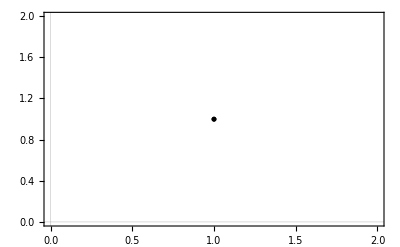

```mathematica
ListLinePlot[Table[{mass/leta,  ADSradius[leta]/horizonsol[mass,leta]}, {leta, 0.01, 1},{mass,0.01,1}], PlotMarkers -> {Automatic, 5},PlotStyle->colorlist[[1]],PlotTheme->"Scientific",PlotRange->Automatic,Frame->True]
```

```mathematica
m01 =AdSminusHorizonPlot[0.1,0.01,1,0.05,1,0.1,0.7];
m02 =AdSminusHorizonPlot[0.3,0.01,1,0.05,2,0.1,0.65];
m03=AdSminusHorizonPlot[0.5,0.01,1,0.05,3,0.1,0.6];
m04=AdSminusHorizonPlot[0.7,0.01,1,0.05,4,0.1,0.55];
```

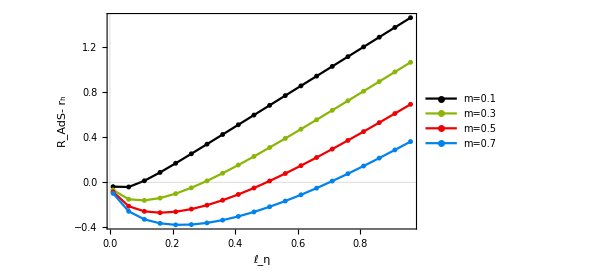

```mathematica
Show[{m01,m02,m03,m04},PlotRange->All,
Frame->True,FrameLabel->{"ℓ_η","R_AdS- r_h"},FrameStyle->Directive[Black,17],
Background->White ,ImageSize->450,
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]
```

It seems that (rought approximation):
 when m>leta  then R_AdS < r_horizon 
 
 Let’s test that also for higher masses and letas ...

```mathematica
m01 =AdSminusHorizonPlot[2,0.01,10,0.1,1,0.1,0.7];
m02 =AdSminusHorizonPlot[3,0.01,10,0.1,2,0.1,0.65];
m03=AdSminusHorizonPlot[5,0.01,10,0.1,3,0.1,0.6];
m04=AdSminusHorizonPlot[7,0.01,10,0.1,4,0.1,0.55];
```

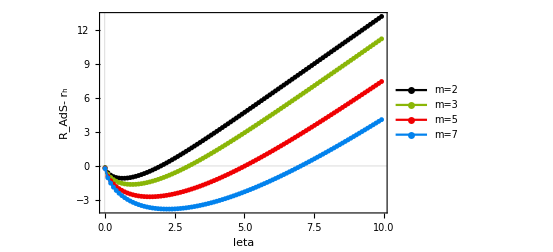

```mathematica
Show[{m01,m02,m03,m04},PlotRange->All,
Frame->True,FrameLabel->{"ℓ_η","R_AdS- r_h"},FrameStyle->Directive[Black,17],
Background->White ,ImageSize->450,
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]
```

```mathematica
7/2.8
```

2.5

```mathematica
m01 =AdSminusHorizonPlot[10,0.01,100,2,1,0.1,0.7];
m02 =AdSminusHorizonPlot[20,0.01,100,2,2,0.1,0.65];
m03=AdSminusHorizonPlot[40,0.01,100,2,3,0.1,0.6];
m04=AdSminusHorizonPlot[50,0.01,100,2,4,0.1,0.55];
```

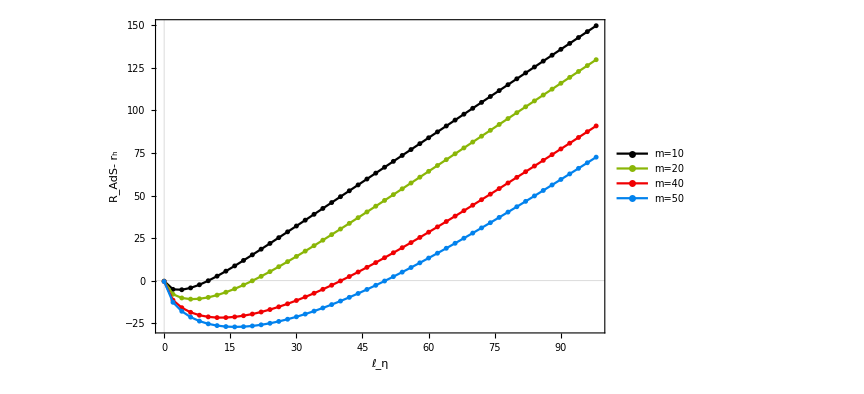

```mathematica
Show[{m01,m02,m03,m04},PlotRange->All,
Frame->True,FrameLabel->{"ℓ_η","R_AdS- r_h"},FrameStyle->Directive[Black,17],
Background->White ,ImageSize->450,
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]
```

```mathematica
20/6//N
```

3.33333

when m>leta  then R_AdS < r_horizon  also for larger masses and letas , as expected !

```mathematica
m01 =AdSminusHorizonPlot[1,1,10000,300,1,0.1,0.7];
(*m02 =AdSminusHorizonPlot[20,0.01,100,2,2,0.1,0.65];
m03=AdSminusHorizonPlot[40,0.01,100,2,3,0.1,0.6];
m04=AdSminusHorizonPlot[50,0.01,100,2,4,0.1,0.55];*)
```

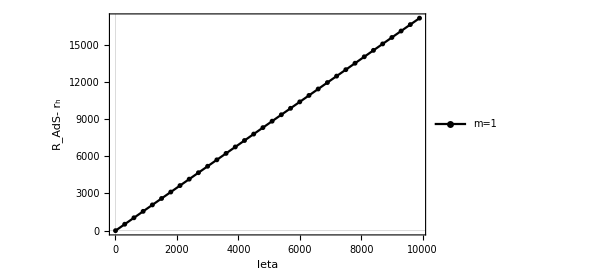

```mathematica
Show[{m01(*,m02,m03,m04*)},PlotRange->All(*{{0,100},{0,200}}*),
Frame->True,FrameLabel->{"ℓ_η","R_AdS- r_h"},FrameStyle->Directive[Black,17],
Background->White ,ImageSize->450,
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]
```

#### r_AdS/r_H

```mathematica
AdSoverHorizon[m_,leta_] :=AdSoverHorizon[m,leta] = horizonsol[m,leta]/ADSradius[leta];
```

```mathematica
AdSoverHorizonPlot[mass_,letastart_,letaend_,letastep_,colorindex_,horizontalposition_,verticalposition_]:=AdSoverHorizonPlot[mass,letastart,letaend,letastep,colorindex,horizontalposition,verticalposition]=ListLinePlot[Table[{leta, AdSoverHorizon[mass, leta]}, {leta, letastart, letaend, letastep}], PlotMarkers -> {Automatic, 5},PlotStyle->colorlist[[colorindex]],PlotTheme->"Scientific",PlotRange->All,Frame->True,PlotLegends->Placed[{Style["m="<>ToString[mass],15]},{Scaled[{horizontalposition,verticalposition}], {0.1,0.1}}]]
```

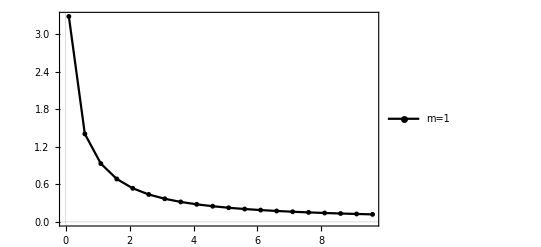

```mathematica
AdSoverHorizonPlot[1,0.1,10,0.5,1,0.5,0.5]
```

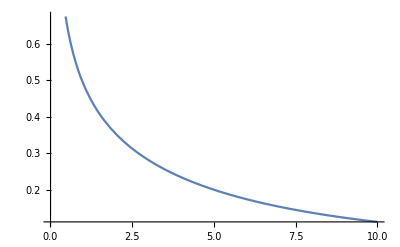

```mathematica
Plot[AdSoverHorizon[5,leta]/5,{leta,0.01,10}]
```

#### Interpolating function r_AdS-r_H

```mathematica
AdSminusHorizonTable[mass_,letastart_,letaend_,letastep_]:=AdSminusHorizonTable[mass,letastart,letaend,letastep]=Table[{leta, AdSminusHorizon[mass, leta]}, {leta, letastart, letaend, letastep}]
```

```mathematica
{m10,m20,m40,m50}=Interpolation[ AdSminusHorizonTable[#,0.01,100,2]]&/@{10,20,40,50}
```

```mathematica
{m2,m3,m5,m7}=Interpolation[ AdSminusHorizonTable[#,0.01,10,0.1]]&/@{2,3,5,7}
```

```mathematica
{m01,m03,m05,m07}=Interpolation[ AdSminusHorizonTable[#,0.01,1,0.01]]&/@{0.1,0.3,0.5,0.7}
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

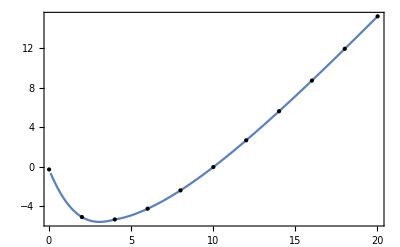

```mathematica
Plot[{m10[x]},{x,0.1,20},Epilog->Point[AdSminusHorizonTable[10,0.01,100,2]],Frame->True]
```

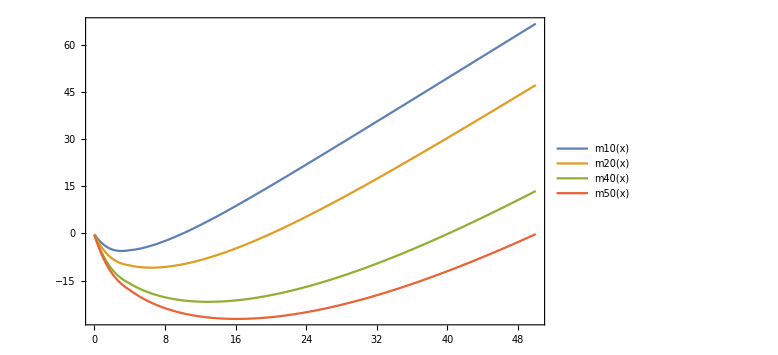

```mathematica
Plot[{m10[x],m20[x],m40[x],m50[x]},{x,0.01,50},PlotLegends->"Expressions",Frame->True,Background->White,ImageSize->Large,PlotRange->All]
```

I zoomed to the plots to see at which points (leta axis-horizontal) the R_Ads -  r_h becomes zero .  Then i calculated the m/leta ratio for these “leta” points. The results are below

```mathematica
{0.1/0.032,0.3/0.0965,0.5/0.1615,0.7/0.2265}//N
```

{3.125,3.10881,3.09598,3.09051}

```mathematica
{2/0.645,3/0.965,5/1.615,7/2.265}//N
```

{3.10078,3.10881,3.09598,3.09051}

```mathematica
{10/3.05,20/6.47,40/12.92,50/16.14}//N
```

{3.27869,3.09119,3.09598,3.09789}

It seems that when m = 3.1*leta then the R_ads = r_h approximately !!!

### Is which plots we have r_H>r_AdS ?

```mathematica
horizonvsADS[#,0.1]&/@{0.03,0.05,0.07,0.1,0.5};
```

mass = 0.03,  coupling = 0.1,   ----- AdS > r_horizon : True ,

mass = 0.05,  coupling = 0.1,   ----- AdS > r_horizon : True ,

mass = 0.07,  coupling = 0.1,   ----- AdS > r_horizon : True ,

mass = 0.1,  coupling = 0.1,   ----- AdS > r_horizon : False ,

mass = 0.5,  coupling = 0.1,   ----- AdS > r_horizon : False ,

```mathematica
horizonvsADS[#,0.1]&/@{0.03,0.05,0.07,0.1,0.5}
```

mass = 0.03,  coupling = 0.1,   Horizon = 0.0596966756,   AdS radius = 0.1732050808,   ----- AdS - r_horizon = 0.113508405 ,  % space = 1.9014192

mass = 0.05,  coupling = 0.1,   Horizon = 0.09734999035,   AdS radius = 0.1732050808,   ----- AdS - r_horizon = 0.0758550904 ,  % space = 0.779199773

mass = 0.07,  coupling = 0.1,   Horizon = 0.1310361096,   AdS radius = 0.1732050808,   ----- AdS - r_horizon = 0.0421689712 ,  % space = 0.321811838

mass = 0.1,  coupling = 0.1,   Horizon = 0.1735982662,   AdS radius = 0.1732050808,   ----- AdS - r_horizon = -0.0003931855 ,  % space = -0.002264916

mass = 0.5,  coupling = 0.1,   Horizon = 0.4265191758,   AdS radius = 0.1732050808,   ----- AdS - r_horizon = -0.253314095 ,  % space = -0.593910214

{Null,Null,Null,Null,Null}

-Graphics-

```mathematica
horizonvsADS[#,0.1]&/@{0.005,0.01,0.025};
```

mass = 0.005,  coupling = 0.1,   ----- AdS > r_horizon : True ,

mass = 0.01,  coupling = 0.1,   ----- AdS > r_horizon : True ,

mass = 0.025,  coupling = 0.1,   ----- AdS > r_horizon : True ,

mass = 0.005,  coupling = 0.1,   Horizon = 0.009999950356,   AdS radius = 0.1732050808,   ----- AdS - r_horizon = 0.16320513 ,  % space = 16.3205941

mass = 0.01,  coupling = 0.1,   Horizon = 0.01999844494,   AdS radius = 0.1732050808,   ----- AdS - r_horizon = 0.153206636 ,  % space = 7.66092745

mass = 0.025,  coupling = 0.1,   Horizon = 0.04986877568,   AdS radius = 0.1732050808,   ----- AdS - r_horizon = 0.123336305 ,  % space = 2.47321703

{Null,Null,Null}

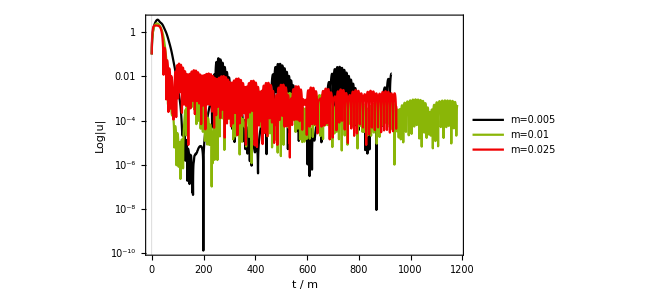

```mathematica
horizonvsADS[#,0.1]&/@{0.005,0.01,0.025}
```

```mathematica
horizonvsADS[#,1]&/@{100,200,500};
```

mass = 100,  coupling = 1,   ----- AdS > r_horizon : False ,

mass = 200,  coupling = 1,   ----- AdS > r_horizon : False ,

mass = 500,  coupling = 1,   ----- AdS > r_horizon : False ,

```mathematica
horizonvsADS[#,1]&/@{100,200,500}
```

mass = 100,  coupling = 1,   Horizon = 13.15612552,   AdS radius = 1.732050808,   ----- AdS - r_horizon = -11.4240747 ,  % space = -0.868346436

mass = 200,  coupling = 1,   Horizon = 16.68544774,   AdS radius = 1.732050808,   ----- AdS - r_horizon = -14.9533969 ,  % space = -0.896193927

mass = 500,  coupling = 1,   Horizon = 22.76031909,   AdS radius = 1.732050808,   ----- AdS - r_horizon = -21.0282683 ,  % space = -0.923900416

{Null,Null,Null}

mass = 0.1,  coupling = 5,   Horizon = 0.1999999744,   AdS radius = 8.66025404,   ----- AdS - r_horizon = 8.46025406 ,  % space = 42.3012757

mass = 0.2,  coupling = 5,   Horizon = 0.3999991845,   AdS radius = 8.66025404,   ----- AdS - r_horizon = 8.26025485 ,  % space = 20.6506792

mass = 0.5,  coupling = 5,   Horizon = 0.9999222468,   AdS radius = 8.66025404,   ----- AdS - r_horizon = 7.66033179 ,  % space = 7.66092745

mass = 1,  coupling = 5,   Horizon = 1.997712953,   AdS radius = 8.66025404,   ----- AdS - r_horizon = 6.66254108 ,  % space = 3.33508429

mass = 2,  coupling = 5,   Horizon = 3.946509125,   AdS radius = 8.66025404,   ----- AdS - r_horizon = 4.71374491 ,  % space = 1.19440872

mass = 5,  coupling = 5,   Horizon = 8.679913312,   AdS radius = 8.66025404,   ----- AdS - r_horizon = -0.0196593 ,  % space = -0.00226492

{Null,Null,Null,Null,Null,Null}

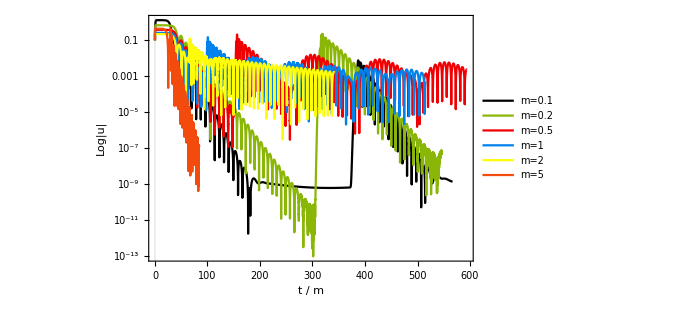

```mathematica
horizonvsADS[#,5]&/@{0.1,0.2,0.5,1,2,5}
```

## Finite Difference Code

### FD - Code

Finite Difference - Implementation CODE

```mathematica
FDrin[start_,stop_,iter_,tfinal_,lam_]:=(
Clear[ψ,Length1,Δrstar,Δt,imax,imin,lambda,jmax,σ,center,ψinit2,ψinit,V];

(*Discretization setup*)
(*rstarmax=stop; rstarmin=start;*) Length1=stop-start;
 Δrstar=Length1/iter; Δt=Δrstar*0.9;
imax=IntegerPart[N[stop/Δrstar]];imin=IntegerPart[N[start/Δrstar]];
jmax = IntegerPart[N[tfinal/Δt]];
(**)
lambda=lam;
(*-------messages to check code behavior-------*)
printstyle={Blue,14,Italic,FontFamily->"Courier"};
Print["leta = ",leta,", m = ",m , ", lambda = ",lambda];
Print["r_horizon = ",horizonsol[leta,a]];
Print[Style["Location of Gaussian's center = ",Blue,14,Italic,FontFamily->"Courier"],Style[x[0],Blue,14,Italic,FontFamily->"Courier"]];
(**)
Print[Style["# of Iterations in space = ",printstyle],Style[iter,14,Blue,Italic]];
(**)
Print[ Style["(r_*)^max =  ",printstyle],Style[stop " , ",printstyle],
Style["r^max =  ",printstyle], Style[NumberForm[ x[stop],20],printstyle]];
Print[ Style["(r_*)^min =  ",printstyle],Style[start " , ",printstyle],
Style[" r^min =  ",printstyle], Style[NumberForm[ x[start],20],printstyle]];
(**)
Print[Style[ "I_max = ",printstyle],Style[imax,printstyle]];
Print[Style[ "I_min = ",printstyle],Style[imin,printstyle]];
(**)
Print[Style["Space Discretization step = ",printstyle],Style[N[Δrstar],printstyle]];
Print[Style["t_final/M = ",printstyle],Style[N[tfinal/m],printstyle]];
Print[Style[ "# of Iterations in time = J_max = ",printstyle],Style[jmax,printstyle]];
Print[Style["Time Discretization step = ",printstyle],Style[Δt,printstyle]];
Print[Style["Δt/(Δr_*) = ",printstyle],Style[N[Δt/Δrstar],printstyle]];(*--V effective & functions A(r)/B(r)Discretization--*)
(*Do[V[i]=Veff[r[i*Δrstar],lam],{i,imin,imax}];
Do[Adis[i]=A[r[i*Δrstar]],{i,imin,imax}];
Do[Bdis[i]=B[r[i*Δrstar]],{i,imin,imax}];*)
(*interVeff=Interpolation[Table[{rstar,Veff[r[rstar],lam]},{rstar,-1000,rstarmax,0.1}],InterpolationOrder->3];*)

V[i_]:=V[i]=SetPrecision[ Veff[x[i*Δrstar],lam],100];

(*--------Initial Condtions--------*) 
σ=0.1;center=0;
ψ[i_,0]:=ψinit2[rstar] /.rstar->i Δrstar  ;
ψinit2[rstar_]:=SetPrecision[1/10 Exp[-(rstar-center)^2/(2 σ^2)],100];
ψ[i_,-1]:=ψinit[x[rstar]]  /.rstar->i Δrstar ;
ψinit[x[rstar_]]=0; 
(*-------Boundary Condition(s)-------*)
ψ[imax,j_]:=ψ[imax,j]= 0;
(*ψ[imin,j_]:=ψ[imin,j]= 0;*)(*comment out when ther is a horizon*)
(*--------Iterating Scheme---------*)

(*SetPrecision[ψ[imax-1,j-1]+(((Adis[imax-1] Bdis[imax-1]+Adis[imax] Bdis[imax])/2 Δt-Δrstar)/((Adis[imax-1] Bdis[imax-1]+Adis[imax] Bdis[imax])/2 Δt+Δrstar))*( ψ[imax-1,j]-ψ[imax,j-1]),40];*)ψ[i_,j_]:=ψ[i,j]=SetPrecision[ -ψ[i,j-2]+(Δt/Δrstar)^2(ψ[i+1,j-1]+ψ[i-1,j-1]) + (2-2 (Δt/Δrstar)^2-V[i] Δt^2) ψ[i,j-1] ,100] ;);
```

## Numerical Results - simulations

Setup - a = 0.5,0,7 (?)

### lambda = 0,

```mathematica
xstarmax
```

4.210278712928110214

```mathematica
Print[x[xstarmax-10^-7]]
```

5.9999×10^7

```mathematica
FDrin[0,xstarmax-10^-7,150,50,0]
```

leta = 1, m = 0.644083, lambda = 0

r_horizon = 1.

Location of Gaussian's center = 1.1

# of Iterations in space = 150

(r_*)^max =  4.35348  , r^max =  5.999904448088104×10^7

(r_*)^min =  0 r^min =  1.1

I_max = 150

I_min = 0

Space Discretization step = 0.0290232

t_final/M = 77.6298

# of Iterations in time = J_max = 1914

Time Discretization step = 0.0261209

Δt/(Δr_*) = 0.9

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];
```

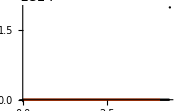
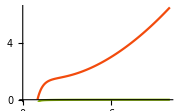

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->Automatic(*{{-10,5},{-0.5,0.5}}*),ImageSize->Small], Show[{VrPlot,Psirplot},ImageSize->Small]}]
```

1.1

General::munfl: 1/(«122»)^852497. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.81 3.458459520888725809235981550077549606555418618300273350979099777504728550891461263057098854531451947×10^-323 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.38 9.881312916824930883531375857364427447301196052286495288511713650013510145404175037305996727232719848×10^-324 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

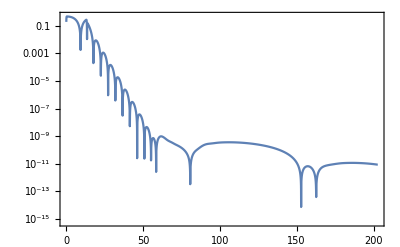

```mathematica
i=0;
(*lambda=5;*)
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,5000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
(* m = 2  code fail *)
Veff[r[-# Δrstar],2] & /@{70,71,72}
r[-# Δrstar]<horizon & /@{70,71,72}
```

{3.42118×10^-13,Indeterminate,-2.11866×10^-14}

{True,False,False}

```mathematica
(* m = 0.2 code fail *)
Veff[r[-# Δrstar],2]&/@ {333,334,335}
r[-334 Δrstar]<horizon
```

{5.28662×10^-14,Indeterminate,-5.12063×10^-14}

False

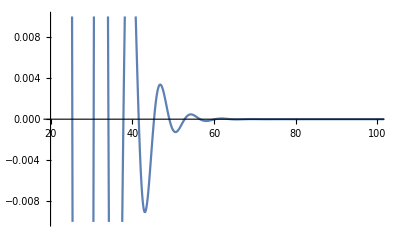

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,5000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Regular_data\\"];
(*Export["GP_Rin_leta"<>ToString[leta]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data1.txt",data];*)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["Regular_leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["Regular_leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.644083 , α = 0.7 , leta = 1 , lambda = 0

File name :

Regular_leta1a0.7l0data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Regular_data\\"];
a05data=Import["Regular_leta1a0.5l0data.txt","Table"]//ToExpression;(*steps = 2000 , t/m = 1000*)
a07data=Import["Regular_leta1a0.7l0data.txt","Table"]//ToExpression;(*steps = 2500 , t/m = 1200*)
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{}
```

{2001,2501,3501,3001,3001,3001,8501,1201,10001,1501}

```mathematica
m0005data[[;;,2]]=Abs[m0005data[[;;,2]]];
m001data[[;;,2]]=Abs[m001data[[;;,2]]];
```

```mathematica
constantline[constant_,range_]:=Plot[constant,{x,0,range},Frame->True,PlotRange->Automatic,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotStyle->Directive[Dashed,Thick,Black]];
```

```mathematica
Print[datalist[[1,320;;330,;;]]//TableForm,Table["  | | |  ",{i,330-320}]//TableForm, m001data[[320;;330,;;]]//TableForm]
```

150.625 | 0.0062512971023679590049093590665
151.097 | 0.0059326650837669952370800885433
151.569 | 0.0053887249500976317634348689012
152.041 | 0.0046444066646831125982908261562
152.513 | 0.0037325158652539280196291926472
152.985 | 0.0026921141118654940901921968077
153.458 | 0.0015665917267775417848207908378
153.93 | 0.00040156224429050606586355520733
154.402 | 0.00075726362709686747924642258312
154.874 | 0.0018660696227747559580723013539
155.346 | 0.0028846694176344056526062331614  | | |  
  | | |  
  | | |  
  | | |  
  | | |  
  | | |  
  | | |  
  | | |  
  | | |  
  | | |  150.625 | -0.0062512971023679590049093590665
151.097 | -0.0059326650837669952370800885433
151.569 | -0.0053887249500976317634348689012
152.041 | -0.0046444066646831125982908261562
152.513 | -0.0037325158652539280196291926472
152.985 | -0.0026921141118654940901921968077
153.458 | -0.0015665917267775417848207908378
153.93 | -0.00040156224429050606586355520733
154.402 | 0.00075726362709686747924642258312
154.874 | 0.0018660696227747559580723013539
155.346 | 0.0028846694176344056526062331614

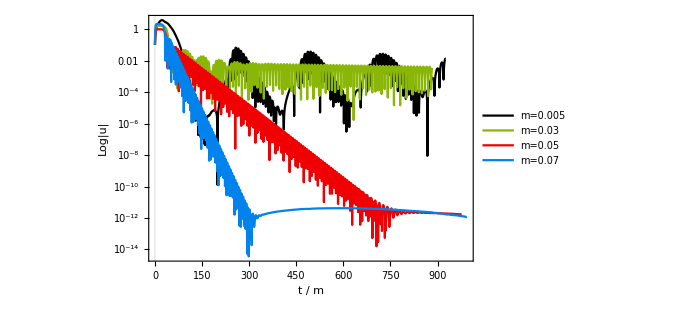

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{m0005data[[;;2000,;;]],m003data[[start;;3000,;;]],m005data[[start;;3000,;;]],m007data[[start;;8500,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["m=0.005",15],Style["m=0.03",15],Style["m=0.05",15],Style["m=0.07",15],Style["m=0.1",15],Style["m=0.2",15]},(*{Scaled[{0.8,0.2}], {0,0}}*)Top],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{30,800},{0,-33}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{m0005data[[;;2000,;;]],m003data[[start;;3000,;;]],m005data[[start;;3000,;;]],m007data[[start;;8500,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{Style["m=0.005",15],Style["m=0.03",15],Style["m=0.05",15],Style["m=0.07",15],Style["m=0.1",15],Style["m=0.2",15]},LegendLayout->{"Row",1}],{Scaled[{0.1,0.85}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{30,800},{2,-33}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

-Graphics-

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

```mathematica
horizonvsADS[#,0.1]&/@{0.005,0.03,0.05,0.07}
```

mass = 0.005,  coupling = 0.1,   --- AdS > r_horizon : True ,

mass = 0.03,  coupling = 0.1,   --- AdS > r_horizon : True ,

mass = 0.05,  coupling = 0.1,   --- AdS > r_horizon : True ,

mass = 0.07,  coupling = 0.1,   --- AdS > r_horizon : True ,

{0.0577347,0.344659,0.56205,0.756537}

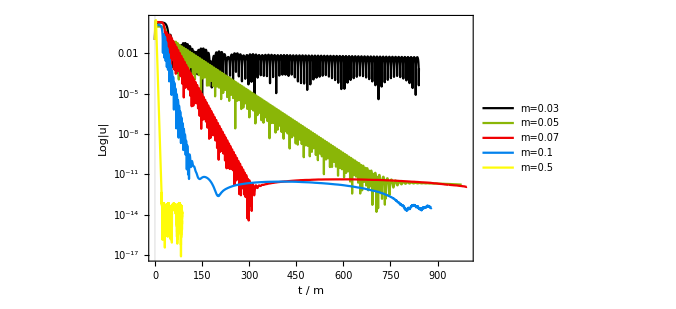

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{(*m0005data[[;;2000,;;]],m001data[[start;;2500,;;]],m00025data[[start;;3500,;;]],*)m003data[[start;;3500,;;]],(*m004data[[start;;3000,;;]],*)m005data[[start;;3000,;;]],m007data[[start;;8500,;;]],m01data[[start;;6000,;;]],m05data[[start;;5500,;;]](*,m07data[[start;;1500,;;]]*)
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{(*Style["m=0.005",15],Style["m=0.01",15],Style["m=0.025",15],*)Style["m=0.03",15],(*Style["m=0.04",15],*)Style["m=0.05",15],Style["m=0.07",15],Style["m=0.1",15],Style["m=0.5",15],Style["m=0.7",15]},Right(*{Scaled[{0.01,0.01}], {0,0}}*)],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,800},{0,-32}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

```mathematica
horizonvsADS[#,0.1]&/@{0.03,0.05,0.07,0.1,0.5}
```

mass = 0.03,  coupling = 0.1,   --- AdS > r_horizon : True ,

mass = 0.05,  coupling = 0.1,   --- AdS > r_horizon : True ,

mass = 0.07,  coupling = 0.1,   --- AdS > r_horizon : True ,

mass = 0.1,  coupling = 0.1,   --- AdS > r_horizon : False ,

mass = 0.5,  coupling = 0.1,   --- AdS > r_horizon : False ,

{0.344659,0.56205,0.756537,1.00227,2.46251}